# Лабораторная работа №5

## Глёза Егор, группа 221701, вариант 1

## 1. Найти приближенные значения производных первого и второго порядков функции в точке , используя: a) функцию D системы Mathematica; б) формулы численного дифференцирования для шага и . Сравнить полученные значения.

Введём функцию  и :

```mathematica
f[x_]:=Tan[Log[3 x]];
x0=2.13;
```

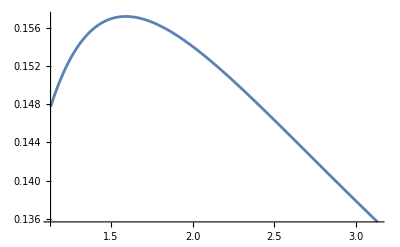

```mathematica
Plot[f[x],{x, x0-1,x0+1}]
```

## Вычислим значение производных функции в точке c помощью функции системы Mathematica:

### Производная первого порядка

```mathematica
D[f[x],x]/. x-> x0
```

5.98241

### Производная второго порядка

```mathematica
D[f[x], {x, 2}]/. x-> x0
```

-22.0576

## Вычислим значение производной функции в точке c помощью формулы численного дифференцирования:

Зададим формулы для приращения функции и вычисления производных:

```mathematica
dy[x_,h_]:=f[x+h]-f[x];
dy[x_,h_,n_]:= If[n == 1,
dy[x,h],
dy[x+h,h,n-1]-dy[x,h,n-1]
];
y1[x_,h_]:=1/h(dy[x,h]-1/2 dy[x,h,2]+1/3 dy[x,h,3]);
y2[x_,h_]:=1/h^2(dy[x,h,2]-dy[x,h,3]);
```

### При :

```mathematica
h =0.1;
y1[x0,h]
y2[x0,h]
```

5.89013

-18.3234

### При :

```mathematica
h =0.01;
y1[x0,h]
y2[x0,h]
```

5.9822

-21.9788

### Сравним полученные значения:

Значения при при  получились достаточно близкими к значениям, полученным при помощи функций системы Mathematica, и точнее, чем при , причём разница между значениями первой и второй производной достаточно различаются, так как формула второй производной имеет второй порядок точности.

## 2. а) Вычислить с помощью формулы второго порядка точности и составить таблицу приближенных значений производной функции на отрезке с шагом . б) Изобразить на одном чертеже (на отрезке ) график функции , полученной с помощью функции D пакета Mathematica, и точки , соответствующие приближенным значениям производной, найденные в пункте а.

Введём функцию :

```mathematica
f[x_]:=Sinh[Log[Cosh[x]]];
```

Зададим границы отрезка и шаг:

```mathematica
a=-1;
b=3;
h=0.2;
```

## а) Вычислить с помощью формулы второго порядка точности и составить таблицу приближенных значений производной функции на отрезке с шагом :

Введём функцию для вычисления значения производной при помощи приближенной формулы для первой производной:

```mathematica
y1[x_,h_]:=(f[x+h]-f[x-h])/(2h);
```

Вычислим и составить таблицу приближенных значений производной функции :

```mathematica
tab=Table[{x,y1[x,h]},{x,a,b,h}];
TableForm[tab, TableHeadings->{None,{x,y}}, Column]
```

x | y
-1. | -0.835793
-0.8 | -0.69139
-0.6 | -0.542088
-0.4 | -0.37772
-0.2 | -0.195081
0. | 0.
0.2 | 0.195081
0.4 | 0.37772
0.6 | 0.542088
0.8 | 0.69139
1. | 0.835793
1.2 | 0.988688
1.4 | 1.1639
1.6 | 1.37461
1.8 | 1.63363
2. | 1.95415
2.2 | 2.35075
2.4 | 2.84035
2.6 | 3.44321
2.8 | 4.18383
3. | 5.09213

## б) Изобразить на одном чертеже (на отрезке ) график функции , полученной с помощью функции D пакета Mathematica, и точки , соответствующие приближенным значениям производной, найденные в пункте а.

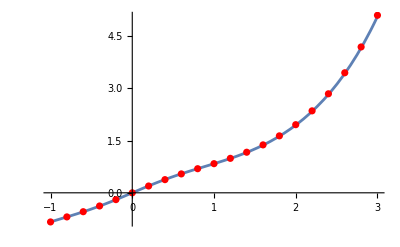

```mathematica
gr1=Plot[D[f[z],z]/.z->x,{x,a,b}];
gr2=ListPlot[tab, PlotStyle->{Red}];
Show[gr1,gr2]
```

## 3. Вычислить определенный интеграл: а) по формуле средних прямоугольников; б) по формуле трапеций. В обоих случаях использовать двойной просчет при и для уточнения значения интеграла по Ричардсону.

Зададим подынтегральную функцию и пределы интегрирования:

```mathematica
f[x_]:=((x^2+6)^(1/3))/(3x+√(x^2+0.6));
a=0.7;
b=1.5;
```

## Вычислим определенный интеграл:

Зададим формулу для уточнения значения по Ричардсону

```mathematica
R[f_,S_,k_,a_,b_,n_,m_]:=S[f,a,b,n]+(S[f,a,b,n]-S[f,a,b,m])/(m^k-n^k)n^k;
```

### а) по формуле средних прямоугольников:

Зададим формулу вычисления определённого интеграла по формуле средних отрезков:

```mathematica
c[i_,n_]:=a+(b-a)/n(i+0.5);
Sm[f_,a_,b_,n_]:=(b-a)/n∑_(i=0)^(n-1) f[c[i+1,n]];
```

#### Вычислим при помощи функции интеграл

```mathematica
R[f,Sm,2,a,b,8,10]
```

0.311199

### а) по формуле трапеций:

Зададим формулу вычисления определённого интеграла по формуле трапеций:

```mathematica
y[f_,a_,b_,n_,i_]:=f[a+(b-a)/n i];
St[f_,a_,b_,n_]:=(b-a)/n(∑_(i=1)^(n-1) y[f,a,b,n,i]+(y[f,a,b,n,0]+y[f,a,b,n,n])/2);
```

#### Вычислим при помощи функции интеграл

```mathematica
R[f,St,2,a,b,8,10]
```

0.344654

## 4. Вычислить определенный интеграл от таблично заданной функции по формуле Симпсона (парабол) для разбиений отрезка интегрирования на 8 и на 16 частей.

Зададим таблично функцию:

```mathematica
data = 
{
{1.2,0.1823},
{1.3,0.2624},
{1.4,0.3365},
{1.5,0.4055},
{1.6,0.4700},
{1.7,0.5306},
{1.8,0.5878},
{1.9,0.6419},
{2,0.6931},
{2.1,0.7419},
{2.2,0.7885},
{2.3,0.8329},
{2.4,0.8755},
{2.5,0.9163},
{2.6,0.9555},
{2.7,0.9933},
{2.8,1.0296}
}
```

{{1.2,0.1823},{1.3,0.2624},{1.4,0.3365},{1.5,0.4055},{1.6,0.47},{1.7,0.5306},{1.8,0.5878},{1.9,0.6419},{2,0.6931},{2.1,0.7419},{2.2,0.7885},{2.3,0.8329},{2.4,0.8755},{2.5,0.9163},{2.6,0.9555},{2.7,0.9933},{2.8,1.0296}}

Зададим функцию для вычисления определённого интеграла по формуле Симпсона:

```mathematica
H[data_]:=(Last[data][[1]]-First[data][[1]])/(Length[data]-1);
H[data_,n_]:=(Last[data][[1]]-First[data][[1]])/n;
Ss[data_,n_]:=H[data,n]/3(First[data][[2]] + Last[data][[2]]+4∑_(i=1)^(n/2-1) data[[(2i H[data, n])/H[data]]][[2]]+2∑_(i=2)^(n/2-1) data[[((2i-1)H[data,n])/H[data]]][[2]]);
```

## Вычислим значение определённого интеграла с использование функции

### Разбиение на восемь частей:

```mathematica
Ss[data,8]
```

0.751873

### Разбиение на шестнадцать частей:

```mathematica
Ss[data,16]
```

0.868023

## 5. Вычислить определенный интеграл с помощью квадратурной формулы Гаусса с n узлами.

Зададим подынтегральную функцию, пределы интегрирования и количество узлов:

```mathematica
f[x_]:=Log[2x]/(4x+1);
a=1.1;
b=2;
n=4;
```

## Вычислим корни полинома Лежандра:

```mathematica
P[n_,x_]:=1/(2^n Factorial[n])D[(x^2-1)^n,{x,n}];
```

```mathematica
t=x/.NSolve[P[4,x]//Simplify]
```

{-0.861136,-0.339981,0.339981,0.861136}

## Вычислим квадратурные коэффициенты:

```mathematica
A=Table[t^i,{i,0,n-1}];
X=Table[Subscript[x, i],{i,1,n}];
B=Table[If[EvenQ[i],0,2/i],{i,1,n}];
A=X/.NSolve[A.X==B]//Flatten
```

{0.347855,0.652145,0.652145,0.347855}

## Вычислим определённый интеграл

```mathematica
S=(b-a)/2∑_(i=1)^n A[[i]]f[(b+a)/2+(b-a)/2 t[[i]]]
```

0.139416